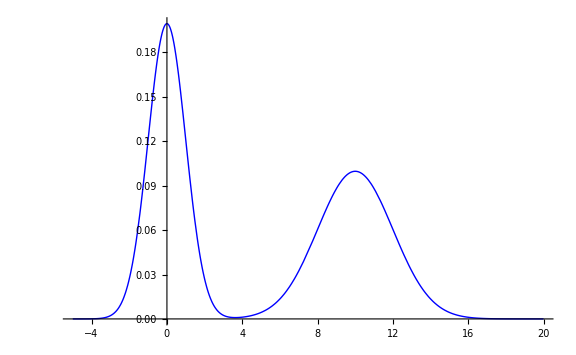

```mathematica
f[x_,μ_,σ_] = 1/(σ*Sqrt[2*Pi])*Exp[-(x-μ)^2/(2*σ^2)];
func[x_] = 
Plot[(f[x,0,1]+f[x,10,2])/2,{x,-5,20},ImageSize->Large,PlotStyle->{{Blue,Thick}},PlotRange->All]
```

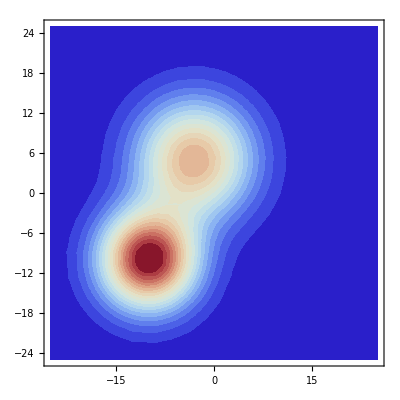

```mathematica
g[x_,y_,μx_,σx_,μy_,σy_] = 1/(σx*σy*Sqrt[2*Pi])*Exp[-(x-μx)^2/(2σx^2)]*Exp[-(y-μy)^2/(2σy^2)];
func[x_,y_] = (g[x,y,-3,6,5,6]+ g[x,y,-10,5,-10,5])/2;
ContourPlot[func[x,y],{x,-25,25},{y,-25,25},ExclusionsStyle->None,PlotRange->All,Contours->20,ContourLines->False,ContourShading->True,ColorFunction->"ThermometerColors"]
```

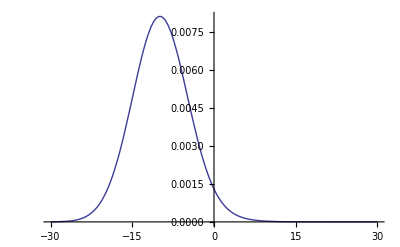

```mathematica
Plot[func[x,-10],{x,-30,30}]
```

```mathematica
MaxValue[func[x,y],{x,y}]
```

MaxValue[1/2 ((ⅇ^(-1/72 (3+x)^2-1/72 (-5+y)^2))/(36 √(2 π))+(ⅇ^(-1/50 (10+x)^2-1/50 (10+y)^2))/(25 √(2 π))),{x,y}]